```mathematica
data=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\SUPPLIMENTARYFIG3.xlsx"];
```

```mathematica
mcmean=Mean[{2694.77,1974.84,2627.28,2869.01,3133.86,3424.65,3039.35,3005.26,3358.64}];
```

```mathematica
YFPmeans={223.1466667,234.358,201.0125,239.6005,255.4105,279.421,218.042,267.2015,237.6005};
```

```mathematica
video1mcherry=data[[1]][[1;;9]];
```

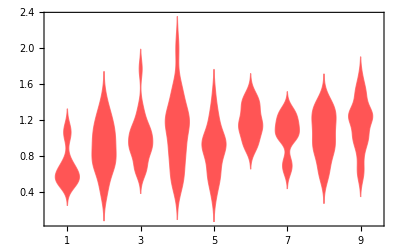

```mathematica
DistributionChart[video1mcherry/mcmean,ChartStyle->Lighter[Red],ChartLabels->{"1","2","3","4","5","6","7","8","9"},FrameStyle->Directive[Black, FontSize->16,Thickness[0.0008]]]
```

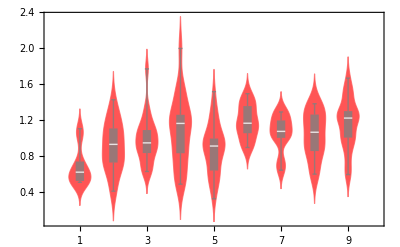

```mathematica
Show[DistributionChart[video1mcherry/mcmean,ChartStyle->Lighter[Red],ChartLabels->{"1","2","3","4","5","6","7","8","9"},FrameStyle->Directive[Black, FontSize->16,Thickness[0.0008]]],
BoxWhiskerChart[video1mcherry/mcmean,BarSpacing->3, ChartStyle->Directive[Gray,Opacity[0.8]]]]
```

```mathematica
video1betax=data[[1]][[10;;18]];
```

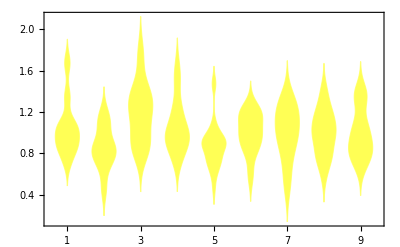

```mathematica
DistributionChart[video1betax/YFPmeans,ChartStyle->Lighter[Yellow],ChartLabels->{"1","2","3","4","5","6","7","8","9"},FrameStyle->Directive[Black, FontSize->16,Thickness[0.0008]]]
```

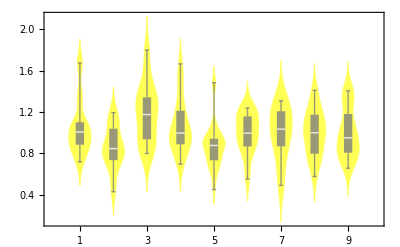

```mathematica
Show[DistributionChart[video1betax/YFPmeans,ChartStyle->Lighter[Yellow],ChartLabels->{"1","2","3","4","5","6","7","8","9"},FrameStyle->Directive[Black, FontSize->16,Thickness[0.0008]]],
BoxWhiskerChart[video1betax/YFPmeans,BarSpacing->3, ChartStyle->Directive[Gray,Opacity[0.8]]]]
```

```mathematica
mcmean2=Mean[{909.88325,861.975,891.1960294,986.3016667,871.7750769,1006.758621,832.3205,809.10725,749.427}];
```

```mathematica
YFPmeans2=Mean[{201.3436282,235.9506596,208.1467935,247.9091156,243.766818,253.2522524,195.6391134,269.180659,192.2611874}];
```

```mathematica
video2mcherry=data[[1]][[20;;28]];
```

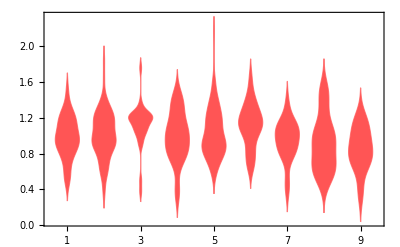

```mathematica
DistributionChart[video2mcherry/mcmean2,ChartStyle->Lighter[Red],ChartLabels->{"1","2","3","4","5","6","7","8","9"},FrameStyle->Directive[Black, FontSize->16,Thickness[0.0008]]]
```

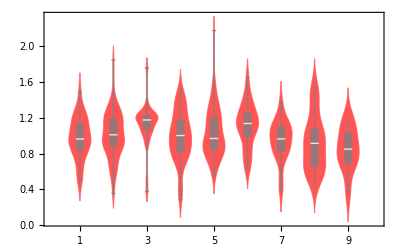

```mathematica
Show[DistributionChart[video2mcherry/mcmean2,ChartStyle->Lighter[Red],ChartLabels->{"1","2","3","4","5","6","7","8","9"},FrameStyle->Directive[Black, FontSize->16,Thickness[0.0008]]],
BoxWhiskerChart[video2mcherry/mcmean2,BarSpacing->3, ChartStyle->Directive[Gray,Opacity[0.8]]]]
```

```mathematica
video2betax=data[[1]][[29;;37]];
```

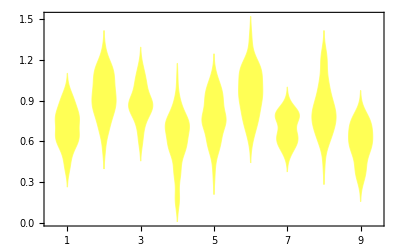

```mathematica
DistributionChart[video2betax/YFPmeans2,ChartStyle->Lighter[Yellow],ChartLabels->{"1","2","3","4","5","6","7","8","9"},FrameStyle->Directive[Black, FontSize->16,Thickness[0.0008]]]
```

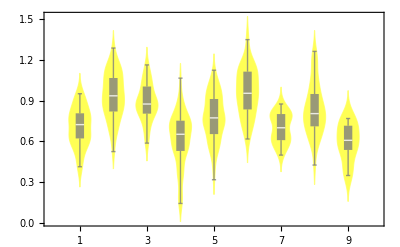

```mathematica
Show[DistributionChart[video2betax/YFPmeans2,ChartStyle->Lighter[Yellow],ChartLabels->{"1","2","3","4","5","6","7","8","9"},FrameStyle->Directive[Black, FontSize->16,Thickness[0.0008]]],
BoxWhiskerChart[video2betax/YFPmeans2,BarSpacing->3, ChartStyle->Directive[Gray,Opacity[0.8]]]]
```